## Differences between primes

```mathematica
(*results={};*)
n=9;primes=allPrimes[[n]];
```

## Prime 9

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
(* Removed first, 2 -> 3, the only transition with d = 1 *)
```

## Visibility Graph

```mathematica
visibles={};Do[
Do[
If[visibleQ[i,j,diffs],AppendTo[visibles,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
igv9=Graph[visibles, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv9];
```

```mathematica
count = Total[adj]//Counts
```

<|16→86,19→53,23→29,36→6,44→3,42→5,80→2,76→1,110→1,111→2,134→1,135→1,142→1,187→1,15→125,10→279,8→484,7→660,14→115,11→214,2→1112,18→58,13→152,20→40,3→1770,9→369,4→1694,17→70,5→1280,6→941,21→24,27→23,29→17,12→177,33→8,26→18,22→31,24→26,39→5,25→22,43→4,32→7,37→8,31→8,64→1,56→2,41→3,30→12,28→11,38→5,35→8,50→2,47→1,52→2,57→2,34→6,71→1,45→2,55→1,49→1,62→1,75→1,48→1,63→1,53→1,1→1|>

```mathematica
count=count[[2;;]]
```

<|19→53,23→29,36→6,44→3,42→5,80→2,76→1,110→1,111→2,134→1,135→1,142→1,187→1,15→125,10→279,8→484,7→660,14→115,11→214,2→1112,18→58,13→152,20→40,3→1770,9→369,4→1694,17→70,5→1280,6→941,21→24,27→23,29→17,12→177,33→8,26→18,22→31,24→26,39→5,25→22,43→4,32→7,37→8,31→8,64→1,56→2,41→3,30→12,28→11,38→5,35→8,50→2,47→1,52→2,57→2,34→6,71→1,45→2,55→1,49→1,62→1,75→1,48→1,63→1,53→1,1→1|>

```mathematica
Sort[count]
```

<|76→1,110→1,134→1,135→1,142→1,187→1,64→1,47→1,71→1,55→1,49→1,62→1,75→1,48→1,63→1,53→1,1→1,80→2,111→2,56→2,50→2,52→2,57→2,45→2,44→3,41→3,43→4,42→5,39→5,38→5,36→6,34→6,32→7,33→8,37→8,31→8,35→8,28→11,30→12,29→17,26→18,25→22,27→23,21→24,24→26,23→29,22→31,20→40,19→53,18→58,17→70,14→115,15→125,13→152,12→177,11→214,10→279,9→369,8→484,7→660,6→941,2→1112,5→1280,4→1694,3→1770|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{19,53/9999},{23,29/9999},{36,2/3333},{44,1/3333},{42,5/9999},{80,2/9999},{76,1/9999},{110,1/9999},{111,2/9999},{134,1/9999},{135,1/9999},{142,1/9999},{187,1/9999},{15,125/9999},{10,31/1111},{8,44/909},{7,20/303},{14,115/9999},{11,214/9999},{2,1112/9999},{18,58/9999},{13,152/9999},{20,40/9999},{3,590/3333},{9,41/1111},{4,154/909},{17,70/9999},{5,1280/9999},{6,941/9999},{21,8/3333},{27,23/9999},{29,17/9999},{12,59/3333},{33,8/9999},{26,2/1111},{22,31/9999},{24,26/9999},{39,5/9999},{25,2/909},{43,4/9999},{32,7/9999},{37,8/9999},{31,8/9999},{64,1/9999},{56,2/9999},{41,1/3333},{30,4/3333},{28,1/909},{38,5/9999},{35,8/9999},{50,2/9999},{47,1/9999},{52,2/9999},{57,2/9999},{34,2/3333},{71,1/9999},{45,2/9999},{55,1/9999},{49,1/9999},{62,1/9999},{75,1/9999},{48,1/9999},{63,1/9999},{53,1/9999},{1,1/9999}}

```mathematica
countrel = countrel[[2;;]]
```

```mathematica
countrel={{23,29/9999},{36,2/3333},{44,1/3333},{42,5/9999},{80,2/9999},{76,1/9999},{110,1/9999},{111,2/9999},{134,1/9999},{135,1/9999},{142,1/9999},{187,1/9999},{15,125/9999},{10,31/1111},{8,44/909},{7,20/303},{14,115/9999},{11,214/9999},{2,1112/9999},{18,58/9999},{13,152/9999},{20,40/9999},{3,590/3333},{9,41/1111},{4,154/909},{17,70/9999},{5,1280/9999},{6,941/9999},{21,8/3333},{27,23/9999},{29,17/9999},{12,59/3333},{33,8/9999},{26,2/1111},{22,31/9999},{24,26/9999},{39,5/9999},{25,2/909},{43,4/9999},{32,7/9999},{37,8/9999},{31,8/9999},{64,1/9999},{56,2/9999},{41,1/3333},{30,4/3333},{28,1/909},{38,5/9999},{35,8/9999},{50,2/9999},{47,1/9999},{52,2/9999},{57,2/9999},{34,2/3333},{71,1/9999},{45,2/9999},{55,1/9999},{49,1/9999},{62,1/9999},{75,1/9999},{48,1/9999},{63,1/9999},{53,1/9999}}
```

{{23,29/9999},{36,2/3333},{44,1/3333},{42,5/9999},{80,2/9999},{76,1/9999},{110,1/9999},{111,2/9999},{134,1/9999},{135,1/9999},{142,1/9999},{187,1/9999},{15,125/9999},{10,31/1111},{8,44/909},{7,20/303},{14,115/9999},{11,214/9999},{2,1112/9999},{18,58/9999},{13,152/9999},{20,40/9999},{3,590/3333},{9,41/1111},{4,154/909},{17,70/9999},{5,1280/9999},{6,941/9999},{21,8/3333},{27,23/9999},{29,17/9999},{12,59/3333},{33,8/9999},{26,2/1111},{22,31/9999},{24,26/9999},{39,5/9999},{25,2/909},{43,4/9999},{32,7/9999},{37,8/9999},{31,8/9999},{64,1/9999},{56,2/9999},{41,1/3333},{30,4/3333},{28,1/909},{38,5/9999},{35,8/9999},{50,2/9999},{47,1/9999},{52,2/9999},{57,2/9999},{34,2/3333},{71,1/9999},{45,2/9999},{55,1/9999},{49,1/9999},{62,1/9999},{75,1/9999},{48,1/9999},{63,1/9999},{53,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.385361/x^1.03304]

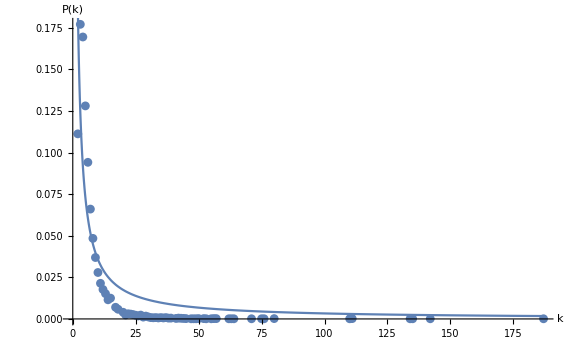

```mathematica
vis9=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[countrel[[All,1]]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-9.eps",vis9];
```

## Mean degree

```mathematica
degree=VertexDegree[igv9]//Mean//N;
```

## Record result

```mathematica
(*AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];*)
```

## Horizontal Visibility Graph

```mathematica
horizontals={};Do[
Do[
If[horizontalQ[i,j,diffs],AppendTo[horizontals,i->j],Null],
{j,i+1,Length@diffs}
],
{i,1,Length@diffs-1}];
```

## Graph

```mathematica
igh9=Graph[horizontals, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh9];
```

```mathematica
count = Total[adj]//Counts
```

<|1→2,4→1406,2→3255,3→2435,5→969,6→631,8→279,7→424,9→185,11→105,10→129,12→61,14→25,13→37,17→11,19→5,18→8,15→15,20→4,16→11,24→1,22→1|>

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}][[2;;]]
```

```mathematica
countrel={{4,1406/9999},{2,1085/3333},{3,2435/9999},{5,323/3333},{6,631/9999},{8,31/1111},{7,424/9999},{9,185/9999},{11,35/3333},{10,43/3333},{12,61/9999},{14,25/9999},{13,37/9999},{17,1/909},{19,5/9999},{18,8/9999},{15,5/3333},{20,4/9999},{16,1/909},{24,1/9999},{22,1/9999}}
```

{{4,1406/9999},{2,1085/3333},{3,2435/9999},{5,323/3333},{6,631/9999},{8,31/1111},{7,424/9999},{9,185/9999},{11,35/3333},{10,43/3333},{12,61/9999},{14,25/9999},{13,37/9999},{17,1/909},{19,5/9999},{18,8/9999},{15,5/3333},{20,4/9999},{16,1/909},{24,1/9999},{22,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x];
```

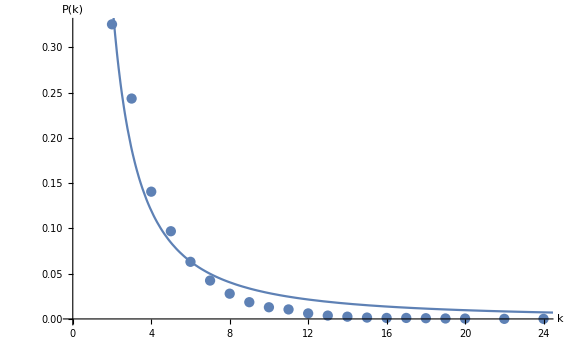

```mathematica
hvis9=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-9.eps",hvis9];
```

## Mean degree

```mathematica
degree=VertexDegree[igh9]//Mean//N;
```

## Record result

```mathematica
(*AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];*)
```

## Return result

```mathematica
results
```

{}